# ABR d’ and Threshold Derivations

## Introduction

In this notebook I derive the d’ and thresholds for three different ways to measure ABR signals: 1) the conventional power of average, 2) correlation with the matched filter, 3) Jackknifed version of correlation.

I did the derivations of the mean and variance of each method by hand, as they involve expectations that I didn’t know how to express in Mathematica.  But given the mean and variance it is simple to write the expressions for d’ and the sound threshold that achieves the desired d’.  Mathematica is good at doing these manipulations.

```mathematica
$Assumptions=s>0&&σ>0 && N>0 && d > 0; (* Can't use assumptions, Root fails.  *)
$Assumptions = {};
```

```mathematica
Import["~/Downloads/ToPython.wl"]
```

## Power Measure

```mathematica
PowerMean[s_, σ_, N_] := s^2 + σ^2/N (* Equation A.8 *)
```

```mathematica
PowerVariance[s_, σ_, N_] := 4*s^2*σ^2/N + 2*σ^4/N^2 (*Equation A.26*)
```

```mathematica
PowerDPrime[s_, σ_, N_]:= (PowerMean[s, σ, N] - PowerMean[0, σ, N])/ Sqrt[(PowerVariance[s, σ, N] + PowerVariance[0, σ, N])/2]
```

```mathematica
PowerDPrimeSimple = Simplify[PowerDPrime[s, σ, N]] //PowerExpand (* Equation A.27 *)
```

(N s^2)/(√2 √(N s^2 σ^2+σ^4))

We now want to know what signal level allows us to reach an arbitrary d’.

```mathematica
PowerThreshold = FullSimplify[Solve[PowerDPrimeSimple == d, s]] (* Equation A.29 *)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{s→-√((d^2 N σ^2-√(d^2 (2+d^2) N^2 σ^4))/N^2)},{s→√((d^2 N σ^2-√(d^2 (2+d^2) N^2 σ^4))/N^2)},{s→-√((d^2 N σ^2+√(d^2 (2+d^2) N^2 σ^4))/N^2)},{s→√((d^2 N σ^2+√(d^2 (2+d^2) N^2 σ^4))/N^2)}}

```mathematica
PowerThresholdSimple = Part[PowerThreshold, 4, 1, 2]//PowerExpand//Simplify
```

(√(d (d+√(2+d^2)) N σ^2))/N

I can’t get MMA’s Asymptotic Function to give me the answer I want, so by inspection it looks like the threshold goes down by 1/Sqrt[N]. Let’s calculate the asymptote as the limit of the threshold multiplied by Sqrt[N], and then divide by the same factor of Sqrt[N]

```mathematica
PowerThresholdAsymptote =Limit[PowerThresholdSimple * Sqrt[N], N -> Infinity]/Sqrt[N]
```

(√(d (d+√(2+d^2)) σ^2))/(√N)

```mathematica
PowerNumTrials = Part[Solve[ Subscript[s, t]== PowerThresholdAsymptote, N], 1, 1, 2]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(d^2 σ^2+d √(2+d^2) σ^2)/s_t^2

### Transformations

```mathematica
ToPython[PowerVariance[s, n, N]/. { σ->n, N->numtrials} ]
```

( 2 * ( n )**( 4 ) * ( numtrials )**( -2 ) + 4 * ( n )**( 2 ) * ( numtrials )**( -1 ) * ( s )**( 2 ) )

```mathematica
ToPython[PowerDPrimeSimple/. { σ->n, N->numtrials} ]
```

( 2 )**( -1/2 ) * numtrials * ( s )**( 2 ) * ( ( ( n )**( 4 ) + ( n )**( 2 ) * numtrials * ( s )**( 2 ) ) )**( -1/2 )

```mathematica
ToPython[PowerThresholdSimple/. { σ->n, N->numtrials}]
```

( numtrials )**( -1 ) * ( d * ( d + ( ( 2 + ( d )**( 2 ) ) )**( 1/2 ) ) * ( n )**( 2 ) * numtrials )**( 1/2 )

```mathematica
TeXForm[PowerDPrimeSimple]
```

\frac{N s^2}{\sqrt{2} \sqrt{N s^2 \sigma ^2+\sigma ^4}}

```mathematica
TeXForm[PowerThresholdAsymptote /. d -> d']
```

\frac{\sqrt{\sigma ^2 d' \left(d'+\sqrt{\left(d'\right)^2+2}\right)}}{\sqrt{N}}

```mathematica
TeXForm[PowerNumTrials /.  d-> d']
```

\frac{\sigma ^2 \left(d'\right)^2+\sigma ^2 d' \sqrt{\left(d'\right)^2+2}}{s_t^2}

```mathematica
PowerNumTrials /. sThreshold->s_t
```

(d^2 σ^2+d √(2+d^2) σ^2)/s_t^2

## Matched Filter Correlation Measure

```mathematica
CorrelationMean[s_, σ_, N_] := s^2 + σ^2/N (* Equation B.5 *)
```

```mathematica
CorrelationVariance[s_, σ_, N_] :=s^2* σ^2* (1+3/N) + (N+1)σ^4/N^2 (* Equation B.23*)
```

```mathematica
CorrelationDPrime[s_, σ_, N_] := (CorrelationMean[s, σ, N] - CorrelationMean[0, σ, N])/Sqrt[(CorrelationVariance[s, σ, N]+ CorrelationVariance[0, σ, N])/2]
```

```mathematica
CorrelationDPrimeSimple = Simplify[CorrelationDPrime[s, σ, N]]*Sqrt[2] //PowerExpand //FullSimplify  ; (* B.29 *)
CorrelationDPrimeSimple = CorrelationDPrimeSimple / Sqrt[2]
```

(√2 N s^2)/(√(N (3+N) s^2 σ^2+2 (1+N) σ^4))

Check the limit, as N->Infinity. Result is a constant, irrespective of N.

```mathematica
CorrelationDPrimeLimit = Limit[CorrelationDPrime[s, σ, N], N -> Infinity]//PowerExpand (* Equation B.30 *)
```

(√2 s)/σ

```mathematica
CorrelationThreshold = Solve[{CorrelationDPrime[s, σ, N] == d}, s]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{s→-1/2 √(d^2 σ^2+(3 d^2 σ^2)/N-√((d^2 (16+9 d^2+16 N+6 d^2 N+d^2 N^2) σ^4)/N^2))},{s→1/2 √(d^2 σ^2+(3 d^2 σ^2)/N-√((d^2 (16+9 d^2+16 N+6 d^2 N+d^2 N^2) σ^4)/N^2))},{s→-1/2 √(d^2 σ^2+(3 d^2 σ^2)/N+√((d^2 (16+9 d^2+16 N+6 d^2 N+d^2 N^2) σ^4)/N^2))},{s→1/2 √(d^2 σ^2+(3 d^2 σ^2)/N+√((d^2 (16+9 d^2+16 N+6 d^2 N+d^2 N^2) σ^4)/N^2))}}

```mathematica
CorrelationThresholdSimple = Part[CorrelationThreshold, 4, 1, 2] //PowerExpand//Simplify(* Select solution with all positive roots *)
```

1/2 √((d (d (3+N)+√(16 (1+N)+d^2 (3+N)^2)) σ^2)/N)

```mathematica
LimitCorrelationTheshold = Limit[CorrelationThresholdSimple, N->Infinity]//PowerExpand
```

(d σ)/(√2)

The derivations above are for a single trial, correlating with the average response we compute from all N trials. But if make a signal-present decision based on all N trials, then the d’ goes up by a factor of Sqrt[N], or equivalently, if we wish to find the sound level that achieves a multi-look d’ of 2, then that is equivalent to the single trial d’ of 2/Sqrt[N].

```mathematica
CorrelationThresholdMulti = PowerExpand[CorrelationThresholdSimple/. d ->  d/Sqrt[N]]//PowerExpand//Simplify
```

(√d √((d (3+N))/(√N)+√(16 (1+N)+d^2 (6+9/N+N))) σ)/(2 N^(3/4))

### Transformations

```mathematica
ToPython[CorrelationVariance[s, σ, N]/. { σ->n, N->numtrials} ]
```

( ( n )**( 4 ) * ( numtrials )**( -2 ) * ( 1 + numtrials ) + ( n )**( 2 ) * ( 1 + 3 * ( numtrials )**( -1 ) ) * ( s )**( 2 ) )

```mathematica
ToPython[CorrelationDPrimeSimple/. { σ->n, N->numtrials} ]
```

( 2 )**( 1/2 ) * numtrials * ( s )**( 2 ) * ( ( 2 * ( n )**( 4 ) * ( 1 + numtrials ) + ( n )**( 2 ) * numtrials * ( 3 + numtrials ) * ( s )**( 2 ) ) )**( -1/2 )

```mathematica
ToPython[CorrelationThresholdSimple/. { σ->n, N->numtrials} ]
```

1/2 * ( d * ( n )**( 2 ) * ( numtrials )**( -1 ) * ( d * ( 3 + numtrials ) + ( ( 16 * ( 1 + numtrials ) + ( d )**( 2 ) * ( ( 3 + numtrials ) )**( 2 ) ) )**( 1/2 ) ) )**( 1/2 )

```mathematica
ToPython[CorrelationThresholdMulti/. { σ->n, N->numtrials} ]
```

1/2 * ( d )**( 1/2 ) * n * ( numtrials )**( -3/4 ) * ( ( d * ( numtrials )**( -1/2 ) * ( 3 + numtrials ) + ( ( 16 * ( 1 + numtrials ) + ( d )**( 2 ) * ( 6 + ( 9 * ( numtrials )**( -1 ) + numtrials ) ) ) )**( 1/2 ) ) )**( 1/2 )

```mathematica
TeXForm[CorrelationDPrimeSimple]
```

\frac{\sqrt{2} N s^2}{\sqrt{2 (N+1) \sigma ^4+N (N+3) s^2 \sigma ^2}}

```mathematica
TeXForm[CorrelationDPrimeLimit]
```

\frac{\sqrt{2} s}{\sigma }

```mathematica
TeXForm[CorrelationThresholdSimple /. d-> d']
```

\frac{1}{2} \sqrt{\frac{\sigma ^2 d' \left((N+3) d'+\sqrt{(N+3)^2 \left(d'\right)^2+16
   (N+1)}\right)}{N}}

```mathematica
TeXForm[LimitCorrelationTheshold]
```

\frac{d \sigma }{\sqrt{2}}

```mathematica
TeXForm[CorrelationThresholdMulti]
```

\frac{\sqrt{d} \sigma  \sqrt{\sqrt{d^2 \left(N+\frac{9}{N}+6\right)+16 (N+1)}+\frac{d
   (N+3)}{\sqrt{N}}}}{2 N^{3/4}}

## Full Correlation Measure

```mathematica
FullMean[s_, σ_, N_] := s^2 + σ^2/N
```

```mathematica
FullVariance[s_, σ_, N_] := 4 *s^2* σ^2 + (N+1)*σ^4/N^2  (* not right yet *)
```

```mathematica
FullDPrime[s_, σ_, N_] := (FullMean[s, σ, N] - FullMean[0, σ, N])/Sqrt[(FullVariance[s, σ, N]+ FullVariance[0, σ, N])/2]
```

```mathematica
FullDPrimeSimple = Simplify[FullDPrime[s, σ, N]] //PowerExpand //FullSimplify
```

(N s^2)/(√(2 N^2 s^2 σ^2+(1+N) σ^4))

### Transformations

```mathematica
ToPython[FullVariance[s, σ, N]/. { σ->n, N->numtrials} ]
```

( ( n )**( 4 ) * ( numtrials )**( -2 ) * ( 1 + numtrials ) + 4 * ( n )**( 2 ) * ( s )**( 2 ) )

```mathematica
FullDPrimeSimple
```

(N s^2)/(√(2 N^2 s^2 σ^2+(1+N) σ^4))

```mathematica
ToPython[FullDPrimeSimple/. { σ->n, N->numtrials} ]
```

numtrials * ( s )**( 2 ) * ( ( ( n )**( 4 ) * ( 1 + numtrials ) + 2 * ( n )**( 2 ) * ( numtrials )**( 2 ) * ( s )**( 2 ) ) )**( -1/2 )

## Jackknife Correlation Measure

```mathematica
JackknifeMean[s_, σ_, N_] := s^2  (* Equation B.55 *)
```

```mathematica
JackknifeVariance[s_, σ_, N_] :=s^2*σ^2*(1 + 1/(N-1)) + σ^4/(N-1) (* Equation B.68 *)
```

```mathematica
JackknifeDPrime[s_, σ_, N_] := (JackknifeMean[s, σ, N] -JackknifeMean[0, σ, N] )/Sqrt[(JackknifeVariance[s, σ, N]+JackknifeVariance[0, σ, N])/2]
```

```mathematica
JackknifeDPrimeSimple= ExpandAll[JackknifeDPrime[s,σ, N]]//Simplify//PowerExpand
```

(√2 √(-1+N) s^2)/(σ √(N s^2+2 σ^2))

```mathematica
Limit[JackknifeDPrimeSimple, N -> Infinity]// PowerExpand//Simplify
```

(√2 s)/σ

```mathematica
JackknifeThreshold = Simplify[ToRadicals[Solve[JackknifeDPrimeSimple == d, s]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{s→-1/2 √((d (d N-√(-16+16 N+d^2 N^2)) σ^2)/(-1+N))},{s→1/2 √((d (d N-√(-16+16 N+d^2 N^2)) σ^2)/(-1+N))},{s→-1/2 √((d (d N+√(-16+16 N+d^2 N^2)) σ^2)/(-1+N))},{s→1/2 √((d (d N+√(-16+16 N+d^2 N^2)) σ^2)/(-1+N))}}

```mathematica
JackknifeThresholdSimple = Part[JackknifeThreshold, 4, 1, 2]//PowerExpand
```

(√d √(d N+√(-16+16 N+d^2 N^2)) σ)/(2 √(-1+N))

```mathematica
Limit[JackknifeThresholdSimple,N->Infinity] //PowerExpand
```

(d σ)/(√2)

```mathematica
JackknifeThresholdMulti = PowerExpand[JackknifeThresholdSimple/. d ->  d/Sqrt[N]]//PowerExpand//ToRadicals//Simplify
```

(√d √(d √N+√(-16+(16+d^2) N)) σ)/(2 √(-1+N) N^(1/4))

```mathematica
Asymptotic[JackknifeThresholdMulti, N->Infinity]
```

(√d √(d+(√((16+d^2) N))/(√N)) σ)/(2 √N)

Again, can’t get Mathematica’s Asymptotic function to get the limit, but it looks like it goes down by Sqrt[N].  Multiply by Sqrt[N] to remove this, find the limit, and then divide by the same quantity.

```mathematica
JackknifeThresholdMultiAsymptote = Limit[JackknifeThresholdMulti*Sqrt[N], N->Infinity]/Sqrt[N]
```

(√d √(d+√(16+d^2)) σ)/(2 √N)

### Transformations

```mathematica
ToPython[JackknifeVariance[s, σ, N]/. { σ->n, N->numtrials}]
```

( ( n )**( 4 ) * ( ( -1 + numtrials ) )**( -1 ) + ( n )**( 2 ) * ( 1 + ( ( -1 + numtrials ) )**( -1 ) ) * ( s )**( 2 ) )

```mathematica
ToPython[JackknifeDPrimeSimple/. { σ->n, N->numtrials}]
```

( 2 )**( 1/2 ) * ( n )**( -1 ) * ( ( -1 + numtrials ) )**( 1/2 ) * ( s )**( 2 ) * ( ( 2 * ( n )**( 2 ) + numtrials * ( s )**( 2 ) ) )**( -1/2 )

```mathematica
ToPython[JackknifeThresholdSimple/. { σ->n, N->numtrials}]
```

1/2 * ( d )**( 1/2 ) * n * ( ( -1 + numtrials ) )**( -1/2 ) * ( ( d * numtrials + ( ( -16 + ( 16 * numtrials + ( d )**( 2 ) * ( numtrials )**( 2 ) ) ) )**( 1/2 ) ) )**( 1/2 )

```mathematica
ToPython[JackknifeThresholdMulti/. { σ->n, N->numtrials}]
```

1/2 * ( d )**( 1/2 ) * n * ( ( -1 + numtrials ) )**( -1/2 ) * ( numtrials )**( -1/4 ) * ( ( d * ( numtrials )**( 1/2 ) + ( ( -16 + ( 16 + ( d )**( 2 ) ) * numtrials ) )**( 1/2 ) ) )**( 1/2 )

```mathematica
TeXForm[JackknifeDPrimeSimple]
```

\frac{\sqrt{2} \sqrt{N-1} s^2}{\sigma  \sqrt{N s^2+2 \sigma ^2}}

```mathematica
TeXForm[JackknifeThresholdSimple]
```

\frac{\sqrt{d} \sigma  \sqrt{\sqrt{d^2 N^2+16 N-16}+d N}}{2 \sqrt{N-1}}

```mathematica
TeXForm[JackknifeThresholdMulti]
```

\frac{\sqrt{d} \sigma  \sqrt{\sqrt{\left(d^2+16\right) N-16}+d \sqrt{N}}}{2 \sqrt{N-1} \sqrt[4]{N}}

## Comparing Power and Jackknife Thresholds

Both the Power measure and the Jackknife (and correlation) methods have asymptotes equal to 1/Sqrt[N].  But the initial constant is different.  We can use Mathematica to solve for their ratio.

```mathematica
PowerJackknifeThresholdRatio = PowerThresholdSimple / JackknifeThresholdMulti//PowerExpand
```

(2 √(d+√(2+d^2)) √(-1+N))/(N^(1/4) √(d √N+√(-16+(16+d^2) N)))

```mathematica
Limit[PowerJackknifeThresholdRatio, N->Infinity]
```

(2 √(d+√(2+d^2)))/(√(d+√(16+d^2)))

```mathematica
Series[PowerJackknifeThresholdRatio, {N,  Infinity, 1}]
```

(2 √(d+√(2+d^2)))/(√((d √N+√((16+d^2) N))/(√N)))-(√(d+√(2+d^2)) (16 d √N+d^3 √N+8 √((16+d^2) N)+d^2 √((16+d^2) N)))/((16+d^2) (d √N+√((16+d^2) N)) √((d √N+√((16+d^2) N))/(√N)) N)+O[1/N]^(5/4)

```mathematica
Asymptotic[(2 Sqrt[d+Sqrt[2+d^2]] Sqrt[-1+N])/(Sqrt[N] Sqrt[d N+Sqrt[-16+16 N+d^2 N^2]]),N->Infinity]
```

(2 √(d+√(2+d^2)))/(√N √(d+(√(d^2 N^2))/N))

```mathematica
ThresholdRatioAsymptote = PowerThresholdAsymptote/JackknifeThresholdMultiAsymptote//PowerExpand
```

(2 √(d+√(2+d^2)))/(√(d+√(16+d^2)))

This plot shows the ratio of the power threshold vs. the correlation (jackknife) threshold. The power measure estimates a sound threshold level that is 1.2 to 2x bigger than that that is needed for the correlation measure.

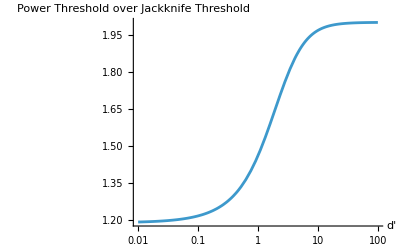

```mathematica
LogLinearPlot[ThresholdRatioAsymptote, {d, 0.01, 100},
			   AxesLabel->{"d'","Power Threshold over Jackknife Threshold"}]
```

```mathematica
ThresholdRatioAsymptote /. d-> 0 ;
```

```mathematica
ThresholdRatioAsymptote /. d-> 1 //N
```

1.46052

```mathematica
ThresholdRatioAsymptote /. d-> 10//N
```

1.96744

### Transformations

```mathematica
ToPython[ThresholdRatioAsymptote]
```

2 * ( ( d + ( ( 2 + ( d )**( 2 ) ) )**( 1/2 ) ) )**( 1/2 ) * ( ( d + ( ( 16 + ( d )**( 2 ) ) )**( 1/2 ) ) )**( -1/2 )

```mathematica
TeXForm[ThresholdRatioAsymptote] /. {d-> d'}
```

\frac{2 \sqrt{d'+\sqrt{\left(d'\right)^2+2}}}{\sqrt{d'+\sqrt{\left(d'\right)^2+16}}}